11

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5}

{ⅇ,2.71488,2.70468,2.68767,2.66387,2.63326,2.59582,2.55155,2.50039,2.4423,2.37717}

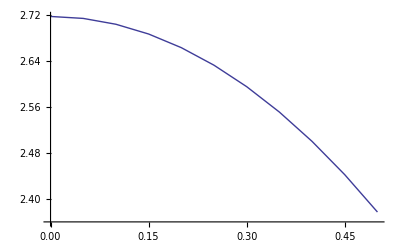

```mathematica
f[x_,y_]:=-(x y)/(√(1-x^2));
y0=ⅇ;
a=0;
b=0.5;
h=0.05;
(*n=(b-a)/h+1;*)
X=Range[a,b,h];
n=Length[X];
Print[n];
Print[X];
Y=Table[{},{n}];
Y2=Table[{},{n}];
Y2[[1]]=y0;
For[i=2,i≤n,i++,
Y[[i]]=Y2[[i-1]]+h*f[X[[i-1]],Y2[[i-1]]];
Y2[[i]]=Y2[[i-1]]+h*(f[X[[i-1]],Y2[[i-1]]]+f[X[[i]],Y[[i]]])/2;
];
Print[Y2];
dots=Table[{},{n}];
For[i=1,i≤n,i++,
dots[[i]]={X[[i]],Y2[[i]]};
]
ListLinePlot[dots]
```

11

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

{{},-1.,-1.01608,-1.04437,-1.08616,-1.14285,-1.21601,-1.30737,-1.41883,-1.5525,-1.7107}

{{},0.9,0.814322,0.73682,0.666713,0.603294,0.545922,0.494019,0.447064,0.404583,0.366148}

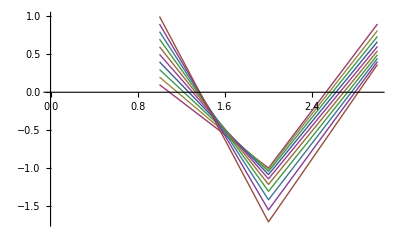

```mathematica
f1[x_,y_,z_]:=1-1/z;(*y'*)
f2[x_,y_,z_]:=1/(y-x); (*z'*)
y0=-1;
z0=1;
a=0;
b=1;
h=0.1;
(*n=(b-a)/h+1;*)
X=Range[a,b,h];
n=Length[X];
Print[n];
Print[X];
Y=Table[{},{n}];
Z=Table[{},{n}];
Y2=Table[{},{n}];
Z2=Table[{},{n}];
Y2[[1]]=y0;
Z2[[1]]=z0;
For[i=2,i≤n,i++,
Y[[i]]=Y2[[i-1]]+h*f1[X[[i-1]],Y2[[i-1]],Z2[[i-1]]];
Z[[i]]=Z2[[i-1]]+h*f2[X[[i-1]],Y2[[i-1]],Z2[[i-1]]];
Y2[[i]]=Y2[[i-1]]+h*(f1[X[[i-1]],Y2[[i-1]],Z2[[i-1]]]+f1[X[[i]],Y[[i]],Z[[i]]])/2;
Z2[[i]]=Z2[[i-1]]+h*(f2[X[[i-1]],Y2[[i-1]],Z2[[i-1]]]+f2[X[[i]],Y2[[i]],Z[[i]]])/2;
];
Print[Y];
Print[Z];
dots=Table[{},{n}];
For[i=1,i≤n,i++,
dots[[i]]={X[[i]],Y[[i]],Z[[i]]};
]
ListLinePlot[dots]
```